```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
fivelisttwo="data";
fivelist="data";
fourlist="data";
threelist="data";
six12="data";
six10="data";
six8="data";
six6="data";
six4="data";
six2="data";
six0="data";
```

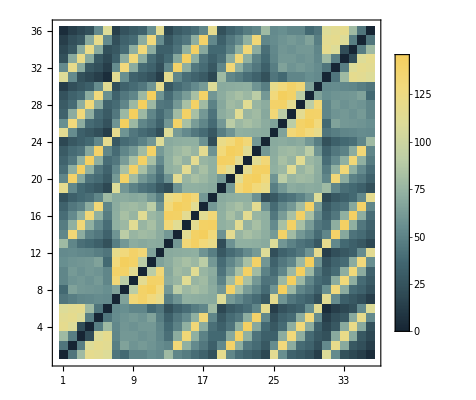

```mathematica
matrix=m612;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
Parallelize[m612=Table[Count[Partition[six12,2],{i,j}],{i,6^2},{j,6^2}];m612=m612+Transpose[m612];
m60=Table[Count[Partition[six0,2],{i,j}],{i,6^2},{j,6^2}];m60=m60+Transpose[m60];
new=ArrayPlot[Reverse[(*#^1/(600-#)^1&/@*)newMatrix-m60],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=6;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 12],
ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]]
```

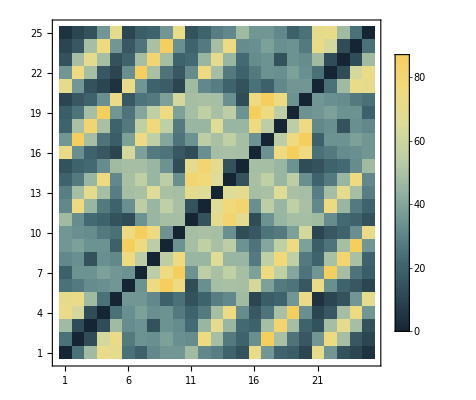

```mathematica
matrix=m514;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
Parallelize[m514=Table[Count[Partition[fivelisttwo[[2]],2],{i,j}],{i,5^2},{j,5^2}];m514=m514+Transpose[m514];
m50=Table[Count[Partition[fivelist[[1]],2],{i,j}],{i,5^2},{j,5^2}];m50=m50+Transpose[m50];
ArrayPlot[Reverse[(*#^1/(300-#)^1&/@*)newMatrix-m50],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=5;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 8],ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]]
```

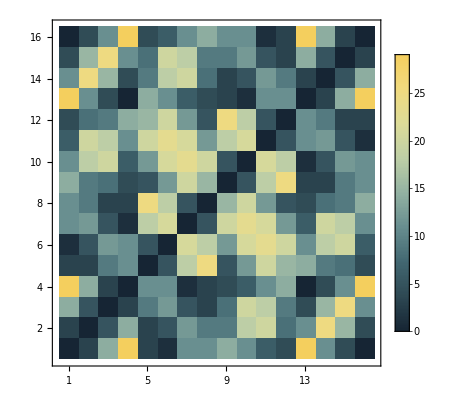

```mathematica
matrix=m410;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
m410=Table[Count[Partition[fourlist[[11]],2],{i,j}],{i,4^2},{j,4^2}];m410=m410+Transpose[m410];
m40=Table[Count[Partition[fourlist[[1]],2],{i,j}],{i,4^2},{j,4^2}];m40=m40+Transpose[m40];
ArrayPlot[Reverse[(*#^1/(90-#)^0&/@*)newMatrix-m40],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=4;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 10],ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]
```

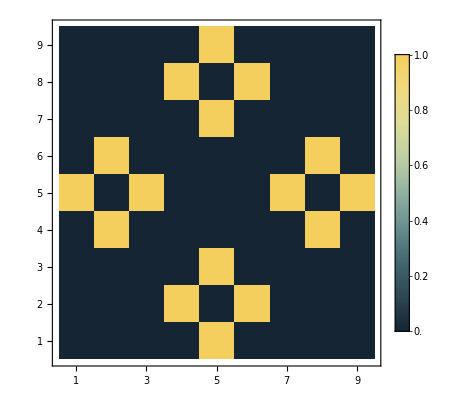

```mathematica
matrix=m310;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
m310=Table[Count[Partition[threelist[[11]],2],{i,j}],{i,3^2},{j,3^2}];m310=m310+Transpose[m310];
m30=Table[Count[Partition[threelist[[1]],2],{i,j}],{i,3^2},{j,3^2}];m30=m30+Transpose[m30];
ArrayPlot[Reverse[newMatrix-m30],ColorFunction->"StarryNightColors"(*,ColorRules->{1->Yellow,0->Black}*),Frame->True,FrameTicks->{d=3;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},TicksStyle->Directive[Thick],FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 12],ColorFunctionScaling->True,PlotLegends->Automatic,PlotLegends->{Automatic,Style[FontFamily->"Times New Roman",FontWeight->Bold, 12]}]
```

```mathematica
l60=Table[Count[six0,i],{i,6^2}];
l62=Table[Count[six2,i],{i,6^2}];
l64=Table[Count[six4,i],{i,6^2}];
l66=Table[Count[six6,i],{i,6^2}];
l68=Table[Count[six8,i],{i,6^2}];
l610=Table[Count[six10,i],{i,6^2}];
l612=Table[Count[six12,i],{i,6^2}];
l50=Table[Count[fivelist[[1]],i],{i,5^2}];
l52=Table[Count[fivelist[[2]],i],{i,5^2}];
l54=Table[Count[fivelist[[3]],i],{i,5^2}];
l56=Table[Count[fivelist[[4]],i],{i,5^2}];
l58=Table[Count[fivelist[[5]],i],{i,5^2}];
l510=Table[Count[fivelist[[6]],i],{i,5^2}];
l512=Table[Count[fivelisttwo[[1]],i],{i,5^2}];
l514=Table[Count[fivelisttwo[[2]],i],{i,5^2}];

l40=Table[Count[fourlist[[1]],i],{i,4^2}];
l42=Table[Count[fourlist[[3]],i],{i,4^2}];
l44=Table[Count[fourlist[[5]],i],{i,4^2}];
l46=Table[Count[fourlist[[7]],i],{i,4^2}];
l48=Table[Count[fourlist[[9]],i],{i,4^2}];
l410=Table[Count[fourlist[[11]],i],{i,4^2}];

l30=Table[Count[threelist[[1]],i],{i,3^2}];
l32=Table[Count[threelist[[3]],i],{i,3^2}];
l34=Table[Count[threelist[[5]],i],{i,3^2}];
l36=Table[Count[threelist[[7]],i],{i,3^2}];
l38=Table[Count[threelist[[9]],i],{i,3^2}];
l310=Table[Count[threelist[[11]],i],{i,3^2}];
```

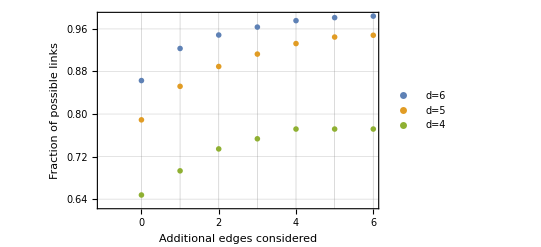

```mathematica
ListPlot[{{N[Mean[l60]/19635],N[Mean[l62]/19635],N[Mean[l64]/19635],N[Mean[l66]/19635],N[Mean[l68]/19635],N[Mean[l610]/19635],N[Mean[l612]/19635]},{N[Mean[l50]/6072],N[Mean[l52]/6072],N[Mean[l54]/6072],N[Mean[l56]/6072],N[Mean[l58]/6072],N[Mean[l510]/6072],N[Mean[l512]/6072]},{N[Mean[l40]/1365],N[Mean[l42]/1365],N[Mean[l44]/1365],N[Mean[l46]/1365],N[Mean[l48]/1365],N[Mean[l410]/1365],N[Mean[l410]/1365]}(*,{N[Mean[l30]/168],N[Mean[l32]/168],N[Mean[l34]/168],N[Mean[l36]/168],N[Mean[l38]/168],N[Mean[l310]/168]}*)},PlotLegends->(Style[#,FontFamily->"Times New Roman",FontWeight->Bold, 12]&/@{"d=6","d=5","d=4"}),Frame->True,FrameTicks->{{All,All},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6}},None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 12],TicksStyle->Directive[Thick],PlotMarkers->"OpenMarkers",FrameLabel->{{"Fraction of possible links",None},{"Additional edges considered ",None}},LabelStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 12],GridLines->Automatic]
```